# Lista 3

## Exercise 1

We want to proof a theorem for a general 3x3 matrix:

```mathematica
ClearAll[A,a,b,c,d,e,f,g,h,i]
A={{a,b,c},{d,e,f},{g,h,i}}
FullSimplify[MatrixPower[A,3]-Tr[A]MatrixPower[A,2]+1/2((Tr[A])^2-Tr[MatrixPower[A,2]])A-Det[A]IdentityMatrix[3]]==0
```

{{a,b,c},{d,e,f},{g,h,i}}

{{0,0,0},{0,0,0},{0,0,0}}==0

## Exercise 2

We want to proof a theorem for two general 2x2 matrices:

```mathematica
ClearAll[A,B,a,b,c,d,e,f,g,h]
A={{a,b},{c,d}}
B={{e,f},{g,h}}
FullSimplify[(Tr[A.B]-Tr[A]Tr[B])IdentityMatrix[2]+Tr[B]A+Tr[A]B-A.B-B.A]//MatrixForm
```

{{a,b},{c,d}}

{{e,f},{g,h}}

(0 | 0
0 | 0)

## Exercise 3

We want to compute rankt of the matrices and find their biggest minor:

```mathematica
M1={{3,1,1,2,-1},{0,2,-1,1,2},{4,3,2,-1,1},{12,9,8,-7,3},{-12,-5,-8,5,1}}
MatrixRank[M1]
Minors[M1,MatrixRank[M1]]
```

{{3,1,1,2,-1},{0,2,-1,1,2},{4,3,2,-1,1},{12,9,8,-7,3},{-12,-5,-8,5,1}}

4

{{18,-8,16,14,0},{0,0,0,0,0},{54,-24,48,42,0},{36,-16,32,28,0},{0,0,0,0,0}}

```mathematica
M2={{1,1,1,1},{4,3,2,1},{1,4,1,1},{5,1,1,1},{1,1,3,1},{1,1,1,2}}
MatrixRank[M2]
Minors[M1,MatrixRank[M2]]
```

{{1,1,1,1},{4,3,2,1},{1,4,1,1},{5,1,1,1},{1,1,3,1},{1,1,1,2}}

4

{{18,-8,16,14,0},{0,0,0,0,0},{54,-24,48,42,0},{36,-16,32,28,0},{0,0,0,0,0}}

## Exercise 4

We present a table witch names of European Capital Cities and their temperature:

```mathematica
TmpCapt=CountryData["Europe","CapitalCity"];
TC=Table[TmpCapt[[i]][[2]][[1]],{i,1,Length[TmpCapt]}];
tc[u_]:=WeatherData[u,"Temperature"];
FinalCT=Map[tc,TC];
FinalData=Transpose[{TC,FinalCT}];
TableForm[FinalData,TableHeadings->{Table[" ",{k,1,Length[FinalData]}],{" "," "}}]
```

|   |  
  | Tirana | 6.
  | AndorraLaVella | 2.2
  | Vienna | 8.5
  | Minsk | 1.8
  | Brussels | 11.5
  | Sarajevo | 2.
  | Sofia | 7.
  | Zagreb | 9.
  | Nicosia | 19.
  | Prague | 6.4
  | Copenhagen | 4.
  | Tallinn | 4.
  | Torshavn | 4.8
  | Helsinki | 2.
  | Paris | 11.
  | Berlin | 5.2
  | Gibraltar | 15.4
  | Athens | 16.4
  | SaintPeterPort | 12.
  | Budapest | 7.3
  | Reykjavik | -1.9
  | Dublin | 11.
  | Douglas | 12.
  | Rome | 15.
  | SaintHelier | 12.
  | Pristina | 7.7
  | Riga | 3.
  | Vaduz | 7.6
  | Vilnius | 2.
  | Luxemburg | 9.
  | Skopje | 2.
  | Valletta | 15.
  | Chisinau | 5.
  | MonacoVille | 9.
  | Podgorica | 6.1
  | Amsterdam | 13.
  | Oslo | 2.7
  | Warsaw | 3.
  | Lisbon | 14.8
  | Bucharest | 7.
  | SanMarino | 20.
  | Belgrade | 11.3
  | Bratislava | 7.
  | Ljubljana | 8.5
  | Madrid | 7.
  | Longyearbyen | 2.2
  | Stockholm | 1.
  | Bern | 3.3
  | Kiev | 1.
  | London | 14.
  | VaticanCity | 15.

## Exercise 5

We want to compute rankt of the matrix:

```mathematica
la={{7-λ,-12,6},{10,-λ-19,10},{12,-24,13-λ}}
Det[la]
MatrixRank[la]
```

{{7-λ,-12,6},{10,-19-λ,10},{12,-24,13-λ}}

-1+λ+λ^2-λ^3

3

## Exercise 6

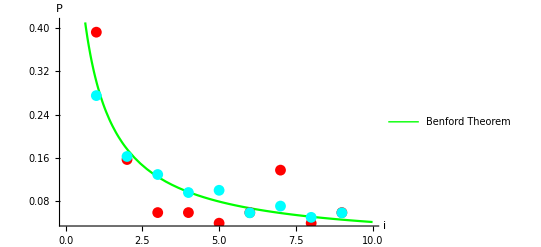

```mathematica
TDigits=Map[RealDigits,FinalCT[[All,1]]];
Dig=Table[TDigits[[i]][[1]][[1]],{i,1,Length[FinalCT]}];
EqN[n_,x_]:=If[n==x,1,0]
Tempd=Table[0,{i,1,9}];
For[k=1,k≤9,k++,For[i=1,i≤Length[Dig],i++,If[Dig[[i]]==k,Tempd[[k]]++,]]];
Tempd=Tempd/Length[Dig]//N;
Temp=ListPlot[Tempd,PlotStyle->Red];

Nms=Table[CountryData[All][[i]][[2]],{i,1,Length[CountryData[All]]}];
GivePop[name_]:=CountryData[name,"Population"]
Pops=Map[GivePop,Nms][[All,1]];
PopDigits=Map[IntegerDigits,Pops][[All]];
DigP=Table[PopDigits[[i]][[1]],{i,1,Length[Pops]}];
Popd=Table[0,{i,1,9}];
For[k=1,k≤9,k++,For[i=1,i≤Length[DigP],i++,If[DigP[[i]]==k,Popd[[k]]++,]]];
Popd=Popd/Length[Pops]//N;
PopPlot=ListPlot[Popd,PlotStyle->Cyan];

Theorem=Plot[Log10[1+1/x],{x,0,10},PlotStyle->Green,AxesLabel->{"i","P"},PlotLegends->{LineLegend[{Green},{"Benford Theorem"}],PointLegend[{Red,Cyan},{"Temperatures","Population"}]}];
Show[Theorem,Temp,PopPlot]
```

## Exercise 7

## Exercise 8

## Exercise 9